# RayTrace2D

Takatoshi Yamada@Ayase corporation
e - mail : takatoshi.yamada@ayasecorporation.com
web cite : https : // www.ayasecorporation.com

# definitions

```mathematica
BeginPackage["AplanaticSinglet`RayTrace2D`"];
```

```mathematica
RayTrace2DVersion="RayTrace2D 0.1A20210318 copyright by Takatoshi Yamada @Ayase corp.";
```

```mathematica
RayTrace2DDescription="RayTrace2D package is for 2dimensional ray trace i.e., ray trace in meridional plane.";
```

```mathematica
RayTrace2DUsage="Needs[\"AplanaticSinglet`RayTrace2D`\"]
createSurface[s1,sphericalShape[0.6],{0.,0}];
createSurface[q1,quadraticShape[0.6,-2.5,{-1,1}],{0.,0}];
createSurface[s2,sphericalShape[-0.3],{0,0.5}];
createSurface[s3,planeShape[],{0,3}];
createConstantMedium[bk7,1.51768];
createOptics[op,{atmosphere,q1,bk7,s2,atmosphere,s3}];
rinp=Table[raySet[{h,-0.3},{Sin[0Degree],Cos[0Degree]}],{h,-0.8,0.8,0.01}];
rs=Map[traceRay[op][#,0.00055]&,rinp];
With[{dom={-0.8,0.8}},Show[surfaceGraphics[q1,dom],surfaceGraphics[s2,dom],Graphics[{Thin,Map[rayLineToDraw[#,4]&,thinOutFromBothSide[rs,12]]}],PlotRange→All,Ticks→None]]";
```

## usage messages

```mathematica
RayTrace2D::usage="RayTrace2D package is for two dimensional strict ray tracing.";
```

### mediums

```mathematica
mediumQ::usage="mediumQ[sym_] returns true if sym is a medium symbol.";
createMedium::usage="createMedium[mediumSymbol_Symbol,rindexFunction_Function,opt___] creates medium symbol. The createMedium function can accept symbol with no Attributes or mediumSymbol[___] style expression.";
```

```mathematica
createConstantMedium::usage="createConstantMedium[mediumSymbol_,rindex_?NumberQ,opt___]";
```

```mathematica
lambdaDomain::usage="mediumNameSymbol[lambdaDomain] returns valid range of wavelength";
```

```mathematica
mediumName::usage="mediumNameSymbol[mediumName] returns printable name if it is set.";
```

```mathematica
refractiveIndexValue::usage="refractiveIndexValue[medium_?mediumQ,lambda_?NumberQ] returns idnex value with wavelength in milli meters.";
```

```mathematica
atmosphere::usage="atmosphere is medium symbol for ideal vacuum, refractive index is exactly 1. DO NOT use vauum or air if you want result of ray trace compatible with Zemax. The definition of 'vacuum' in Zemax is different from general physical meaning i.e., electromagnetic field in free space.";
```

```mathematica
createMediumsFromAGFFile::usage="createMediumsFromAGFFile[path_String] reads Zemax AGF format file and create mediums in the file and returns catalogName string. Medium symbols are all changed to lower case and '-' or '_' etc. to '$' character because symbols should follow the Mathematica input syntax.";
```

```mathematica
createMediumsFromAGFString::usage="createMediumsFromAGFString[agfString_String,catalogname_String] creates  mediums in the string and returns catalogName string. Medium symbols are all changed to lower case and '-' or '_' etc. to '$' character because symbols should follow the Mathematica input syntax.";
```

```mathematica
mediumCatalog::usage="mediumCatalog[] returns list of medium catalogNamess already read. mediumCatalog[catalogName_String] returns list of medium names. mediumCatalog[mediumName_String] returns a symbol for medium with 'mediumName'.";
```

### rays

```mathematica
ray::usage="ray is a container symbol of ray a component ray[___].";
```

```mathematica
stoppedRay::usage="stoppedRay is a container symbol a ray that can not be traced.";
```

```mathematica
raySet::usage="raySet[{y0_,z0_},{yd_,zd_},opt___] or raySet[{y0_,z0_},angleToAxis_?NumericQ,refractiveIndex_?NumericQ,opt___] create ray object. It can be called to create initial object.";
```

```mathematica
appendRayOption::usage="appendRayOption[ray[__],opt___] appends new option 'opt'to a ray.";
```

```mathematica
markRayAsDomainDefinedMarginal::usage="markRayAsDomainDefinedMarginal[r_ray] returns a ray object marked as a marginal ray. A surface reached by this ray redefine its domain for the ray as a marginal.";
```

```mathematica
raySetAsDomainDefinedMarginal::usage="raySetAsDomainDefinedMarginal[{y0_,z0_},{yd_,zd_},opt___] returns a ray object marked as a marginal ray. A surface reached by this ray redefine its domain for the ray as a marginal.";
```

```mathematica
origin::usage="origin[ray[___]]";
direction::usage="direction[ray[org_,dir_,___]]:=dir";
raySequence::usage="container object of rays.";
raySegmentCount::usage="raySegmentCount[rs_raySequence] returns number of ray segments.";
sequenceOfRays::usage="sequenceOfRays[rs_raySequence] returns a list of ray segments excluding stopped ray.";
```

### raySequence

```mathematica
rayLineToDraw::usage="rayLineToDraw[raySequence[___]] returns Line[] object for Graphics. rayLineToDraw[raySequence[___],count_] line with rays upto 'count'.rayLineToDraw[raySequence[___],{from_,upto_}] rays line with 'from' to 'upto' rays.";
```

```mathematica
opticalPathDifference::usage="opticalPathDifference[{raySequence[__]...}] returns list of OPD with input ray height.";
opticalPathLengthForHeight::usage="opticalPathLengthForHeight[rs_raySequence]";
```

```mathematica
logitudinalAberPositionReversed::usage="logitudinalAberPositionReversed[raySequence[__]] returns list of {_,_} to draw lateral aberration.";
```

```mathematica
longitudinalSphericalAberration::usage="longitudinalSphericalAberration[rs:{__raySequence},op_?opticsQ] returns two-dimensional coordinates of longitudinal spherical aberration to draw longitudinal spherical aberration plot.";
```

```mathematica
oscValueReversed::usage="oscValueReversed[raySequence[__],f_] returns OSC with focal length 'f'.";
```

```mathematica
offenceAgainstSineCondition::usage="offenceAgainstSineCondition[rs:{__raySequence},f_] returns two-dimensional coordinates of offence against the sine condition to draw OSC plot. The function requires focal length 'f'. For finite conjugate, offenceAgainstSineCondition[rs:{__raySequence},{dop_,dpi_}] can be called. The function requires paraxial distance from object to principal plane in object side 'dop' and paraxial distance from principal plane in image side to image 'dpi'.";
```

### shapes,surfaces,optics

```mathematica
unfoldInterpolation::usage="unfoldInterpolation[if_InterpolatingFunction] is for surface shape interpolation function to enhance domain {0,maxHeight} to {-maxHeight,maxHeight}.";
```

```mathematica
opticsTags={surfaces,mediums};
surfaceTags={shape,origin};
shapes={plane,perfectThinLens,spherical,quadratic,parametric};
```

```mathematica
shapeQ::usage="shapeQ[s_Symbol] returns True if symbol 's' is a shape symbol.";
surfaceQ::usage="suraceQ[s_Symbol] returns True if symbol 's' is a surface symbol.";
opticsQ::usage="opticsQ[s_Symbol] returns True if symbol 's' is an optics symbol.";
```

#### shapes

```mathematica
planeShape::usage="planeShape[] returns a plane shape object at z=0";
```

```mathematica
perfectThinLensShape::usage="perfectThinLensShape[f_] returns a perfect thin lens with focal length 'f'.";
```

```mathematica
sphericalShape::usage="sphericalShape[curv_] or sphericalShape[curv_,dom:{_,_}] returns spherical shape object ";
```

```mathematica
quadraticShape::usage="quadraticShape[curv_,conic_,dom:{_,_}] or quadraticShape[curv_,conic_] returns quadratic shape object'";
```

```mathematica
parametricShape::usage="parametricShape[f_Function,dom:{_,_}] or parametricShape[f_InterpolatingFunction] returns parametric shape object.";
```

#### surfaces

```mathematica
createSurface::usage="createSurface[surfaceSymbol_,surfaceShape_,position:{_,_},opt___] assigns surface object to the symbol 'surfaceSymbol'. createSurface can accept symbol with no Attributes or surfaceSymbol[___] style expression.";
```

```mathematica
surfaceComment::usage="surfaceComment is an option of createSurface and set comment string. To read it evaluate surfaceSymbol[surfaceComment].";
```

```mathematica
attachAttributeToSurface::usage="attachAttributeToSurface[surfaceSymbol_?surfaceQ,attributeSymbol_Symbol,attributeValue_] set an attriburte to a surface. The attribute can be accessed surfaceSymbol[attributeSymbol].";
```

```mathematica
positionOfAttributedSurface::usage="positionOfAttributedSurface[op_?opticsQ,attributeSymbol_Symbol,attributeValue_] returns position numbers of surfaces with 'attributeSymbol' attribute set to attributeValue.";
```

```mathematica
marginalPositionOfSurface::usage="marginalPositionOfSurface[s_surfaceQ] returns edge positions of the surface.";
```

```mathematica
clearAperture::usage="clearAperture[surf_?surfaceQ] returns 2D clear aperture size.";
```

```mathematica
surfacePosition::usage="surfacePosition[surf_?surfaceQ] returns the surface position along the optical axis.";
```

```mathematica
surfaceShapeType::usage="surfaceShapeType[surf_?surfaceQ] returns shape head symbol.";
```

#### optics

```mathematica
createOptics::usage="createOptics[opticsSymbol_,seq:{___}] assigns optics object to the symbol 'oticsSymbol'.  The createOptics function can accept symbol with no Attributes or opticsSymbol[___] style expression. The argument 'seq' is a list of medium, surface, medium, surface, ...";
```

```mathematica
setPupil::usage="setPupil[opticsSymbol_?opticsQ,surfaceSymbol_?surfaceQ] sets 'surfaceSymbol' surface to pupil of optical system.";
```

```mathematica
pupilSurface::usage="pupilSurface is a surface attribute specifing pupil.";
```

### ray tracing and others

```mathematica
traceRay::usage="traceRay[optics_][initialRay_ray,lambda_?NumberQ] traces the ray through optics at wavelength lambda, and returns raySequence object.";
```

```mathematica
interpolationDomain::usage="interpolationDomain[itf_InterpolatingFunction] returns doian of scalar interpolating function 'itf',";
```

```mathematica
interpolationSectionPoints::usage="interpolationSectionPoints[itf_InterpolatingFunction] returns list of anchor points of interpolation of scalar function.";
```

```mathematica
thinOutFromBothSide::usage="thinOutFromBothSide[lis_List,n_] returns new list of element count to n from Length[lis].";
```

```mathematica
surfaceGraphics::usage="surfaceGraphics[s_?surfaceQ,dom:{_,_}] returns Graphics object of the surface.";
```

```mathematica
opticsGraphics::usage="opticsGraphics[opt_?opticsQ,opt___Rule] returns Graphics object of all surfaces.";
```

```mathematica
hideUselessSurface::usage="hideUselessSurface is an option of opticsGraphics and opticsGraphics. If hideUselessSurface.10.08.08.08->False, the a surface sandwitched same medium is shown opticsGraphics. Default value is True.";
```

```mathematica
rayCongruenceGraphics::usage="rayCongruenceGraphics[rss:{__raySequence},opt___Rule] returns Graphics object of rays.";
```

```mathematica
removeLast::usage="removeLast is an option of opticsGraphics and rayCongruenceGraphics. If removeLast->True, the last surface and ray segments toward the last surface are not drawn.";
```

```mathematica
rayCount::usage="rayCount is an option of rayCongruenceGraphics.";
```

## Private section

```mathematica
Begin["`Private`"];
```

## Internal definitions

```mathematica
canBeObjectSymbol[s_Symbol]:=ContainsOnly[Attributes[s],{Temporary}]
canBeObjectSymbol[s_Symbol[___]]:=canBeObjectSymbol[s]
canBeObjectSymbol[_]:=False
```

### medium

```mathematica
mediumTypes={constantMedium,dispersiveMedium};
Options[createMedium]={mediumName->"",lambdaDomain->All};
refractiveIndexValue::outofrange="wavelength `1` is not in range `2` to `3`";
createMedium[mediumSymbol_?canBeObjectSymbol,rindexFunction_Function,opt___]:=Module[{},
mediumQ[mediumSymbol]^=True;
mediumSymbol[mediumType]=dispersiveMedium;
mediumSymbol[mediumName]=mediumName/.{opt}/.mediumName->ToString[mediumSymbol];
mediumSymbol[lambdaDomain]=lambdaDomain/.{opt}/.Options[createMedium];
mediumSymbol[refractiveIndex]=rindexFunction;
mediumSymbol[lastLambda]=0.0;
mediumSymbol[lastIndex]=0.0;
refractiveIndexValue[mediumSymbol]^=Function[{lambda},Evaluate[If[(mediumSymbol[lambdaDomain]=!=All)&&Not[Between[lambda,medium[lambdaDomain]]],Message[refractiveIndexValue::outofrange,lambda,mediumSymbol[lambdaDomain][[1]],mediumSymbol[lambdaDomain][[-1]]];Return[$Failed]];
If[lambda=!=mediumSymbol[lastLambda],
mediumSymbol[lastLambda]=lambda;
mediumSymbol[lastIndex]=mediumSymbol[refractiveIndex][lambda]];
mediumSymbol[lastIndex]]];
mediumSymbol
]
createConstantMedium[mediumSymbol_?canBeObjectSymbol,rindex_?NumberQ,opt___]:=Module[{},
mediumQ[mediumSymbol]^=True;
refractiveIndexValue[mediumSymbol]^=Function[{lambda},mediumSymbol[lastIndex]];
mediumSymbol[mediumType]=constantMedium;
mediumSymbol[mediumName]=mediumName/.{opt}/.{mediumName->ToString[mediumSymbol]};
mediumSymbol[lambdaDomain]=All;
mediumSymbol[lastLambda]=0.0;
mediumSymbol[lastIndex]=rindex;
mediumSymbol
]
mediumQ[_]:=False
```

```mathematica
refractiveIndexValue[medium_?mediumQ,lambda_?NumberQ]:=refractiveIndexValue[medium][lambda]
```

```mathematica
createConstantMedium[atmosphere,1.0];
```

```mathematica
sellmeierDispersion[a1_,b1_,a2_,b2_,a3_,b3_,___]:=Function[{lambda},With[{lsq=(1000lambda)^2},Sqrt[1+(a1/(lsq-b1)+a2/(lsq-b2)+a3/(lsq-b3))lsq]]]
```

```mathematica
schottDispersion[a0_,a1_,a2_,a3_,a4_,a5_,___]:=Function[{lambda},With[{lsq=(1000lambda)^2},Sqrt[a0+a1*lsq+(a2+(a3+(a4+a5/lsq)/lsq)/lsq)/lsq]]]
```

```mathematica
conradyDispersion[a_,b_,c_,___]:=Function[{lambda},With[{l=1000lambda},a+b/l+c/l^3.5]]
```

```mathematica
interpretNumeric::cannotconvert="A non-numerical string is found in `1`";interpretNumeric[s_String]:=With[{n=ToExpression[StringReplace[s,"E"->"*10^"]]},If[! NumberQ[n],Message[interpretNumeric::cannotconvert,s],n]]
```

```mathematica
dispersionFunctionFromString[s_String,modelFunction_]:=Module[{sp},
sp=StringSplit[s];
If[Length[sp]===0||First[sp]=!="CD",Return[$Failed]];
Apply[modelFunction,Map[interpretNumeric,Rest[sp]]]
]
```

```mathematica
$nameHeader="NM*";
$disersionCoefficientHeader="CD*";
$lambdaRangeHeader="LD*";
```

```mathematica
Clear[dispersionModels];
dispersionModels[1]=schottDispersion;dispersionModels[2]=sellmeierDispersion;
dispersionModels[5]=conradyDispersion;
dispersionModels[_]:=$Failed;
```

```mathematica
headerMatchQ[s_String,header_String]:=StringMatchQ[s,header]
```

```mathematica
rangeFind[{}]:=All
rangeFind[{s_String}]:=With[{ws=StringSplit[s]},{0.001interpretNumeric[ws[[2]]],0.001interpretNumeric[ws[[3]]]}]
```

```mathematica
readDispersion[strs:{_String...}]:=Module[{frst,name,dispf,dlin,rlin,rng},
frst=StringSplit[strs[[1]]];
name=frst[[2]];
dispf=dispersionModels[ToExpression[frst[[3]]]];
If[dispf==$Failed,Return[$Failed]];
dlin=Flatten[Select[strs,headerMatchQ[#,$disersionCoefficientHeader]&]][[1]];
rlin=rangeFind[Flatten[Select[strs,headerMatchQ[#,$lambdaRangeHeader]&]]];
{name,ToExpression[toMediumSymbol[name]],dispersionFunctionFromString[dlin,dispf],rlin}
]
```

```mathematica
toMediumSymbol[s_String]:=Module[{sl},
sl=If[StringMatchQ[s,RegularExpression["\\d"]],"$",""]<>ToLowerCase[s];
StringReplace[sl,{"-"->"$","_"->"$"}]
]
```

```mathematica
mediumCatalog[]={};
Clear[createMediumsFromAGFFile];
createMediumsFromAGFFile::cannotopen="can not open the path `1`";
createMediumsFromAGFFile[path_String]:=Module[{catalogName(*,strs,lines,rlines,blck,ps*)},
If[Not[StringMatchQ[FileExtension[path],"AGF",IgnoreCase->True]],Message[parseStringForDispersion::cannotopen,path];Return[$Failed]];
strs=ReadList[path,String,RecordSeparators->{"\n","\r\n","\r"}];
If[strs===$Failed,Message[parseStringForDispersion::cannotopen,path];Return[$Failed]];
createMediumsFromAGFString[strs,FileBaseName[path]]
]
```

```mathematica
createMediumsFromAGFString[agfstrs:{_String...},catalogName_String]:=Module[{strs,lines,rlines,blck,ps},
(*catalogName=FileBaseName[catName];*)
strs=Map[StringReplace[#,RegularExpression["[[:cntrl:]]"]:>""]&,agfstrs];
lines=SequenceSplit[strs,{x_?(headerMatchQ[#,$nameHeader]&)}:>{x}];
rlines=If[headerMatchQ[lines[[1,1]],$nameHeader],lines,Rest[lines]];
blck=Map[Flatten,Partition[rlines,2]];
ps=Select[Map[readDispersion,blck],#=!=$Failed&];
AppendTo[mediumCatalog[],catalogName];
mediumCatalog[catalogName]=Map[First,ps];
Map[createMedium[#[[2]],#[[3]],mediumName->#[[1]],lambdaDomain->#[[4]]]&,ps];
ReleaseHold[Map[Hold[mediumCatalog[#[[1]]]=#[[2]]]&,ps]];
catalogName
]
```

### ray

```mathematica
raySet[{y0_,z0_},{yd_,zd_},opt___]:=ray[{y0,z0},{yd,zd},opt]
raySet[{y0_,z0_},angleToAxis_?NumericQ,refractiveIndex_?NumericQ,opt___]:=ray[{y0,z0},{refractiveIndex*Sin[angleToAxis],refractiveIndex*Cos[angleToAxis]},opt]
```

```mathematica
appendRayOption[ray[p_,d_,o___],opt___]:=ray[p,d,o,opt]
```

```mathematica
objectSidePrincipalPointPosition[wl_,solverResult:{__Rule}]:=With[{n=(refractiveIndexValue[lensMediumSymbol/.solverResult][wl])},
-((lensMediumThickness*frontSurfaceCurvature)/(lensMediumThickness*frontSurfaceCurvature*backSurfaceCurvature*(-1+n)+(frontSurfaceCurvature-backSurfaceCurvature)*n))/.solverResult]
```

```mathematica
Clear[domainDefinedMarginalRay];
```

```mathematica
markRayAsDomainDefinedMarginal[r_ray]:=appendRayOption[r,domainDefinedMarginalRay]
raySetAsDomainDefinedMarginal[{y0_,z0_},{yd_,zd_},opt___]:=raySet[{y0,z0},{yd,zd},domainDefinedMarginalRay,opt]
domainDefinedMarginalRayQ[ray[{_,_},{_,_},opt___]]:=MemberQ[{opt},domainDefinedMarginalRay]
```

```mathematica
setRefractiveIndexForRay[ray[p:{_,_},v:{_,_},opt___],index_]:=With[{len=Sqrt[v.v]},ray[p,Map[index/len*#&,v],opt]]
```

```mathematica
(*ray[org:{y0_,z0_},dir:{yd_,zd_},___]*)
origin[ray[org_,dir_,___]]:=org
heightOfOrigin[ray[{h_,z_},_,___]]:=h
direction[ray[org_,dir_,___]]:=dir
offsetRay[ray[{y_,z_},dir_,opt___],{yoff_,zoff_}]:=ray[{y-yoff,z-zoff},dir,opt]
```

```mathematica
origin[stoppedRay[org:{_,_},__]]:=org
origin[stoppedRay[noIntersection]]:=Sequence[]
```

```mathematica
parallelToAxisQ[ray[{_,_},{yd_,_},___]]:=(N[yd]===0.0)
(*declinationForHeight[r_ray]:=Indeterminate/;parallelToAxisQ[r]*)
declinationForHeight[r:ray[{_,_},{yd_,_},___]]:=yd
signOfCosine[r:ray[{_,_},{_,zd_},___]]:=Sign[zd]
```

```mathematica
offsetBackRay[ray[{y_,z_},dir_,opt___],{yoff_,zoff_}]:=ray[{y+yoff,z+zoff},dir,opt]
offsetBackRay[stoppedRay[noIntersection],{yoff_,zoff_}]:=stoppedRay[noIntersection]
offsetBackRay[stoppedRay[{y_,z_},a_],{yoff_,zoff_}]:=stoppedRay[{y+yoff,z+zoff},a]
```

```mathematica
refractiveIndexFromDirection[ray[_,dir_,___]]:=Sqrt[dir.dir]
```

```mathematica
axisCrossingPosition[ray[{y_,z_},{s_,c_},___]]:=(s*z-c*y)/s
axisCrossingPosition[ray[{y_,z_},{s_?(N[#]===0.0&),c_},___]]:=Indeterminate
```

### raySequence

```mathematica
raySegmentCount[raySequence[lambda_,rays_List]]:=Length[rays]
```

```mathematica
opticalPath[{p1:{_,z1_},p2:{_,z2_}},refInd_]:=With[{v=p1-p2},Sign[z2-z1]*Sqrt[v.v]refInd](*assumed rays go toward positive z direction*)
```

```mathematica
(*raySequence[lambda_,rays:{ray[___]...}]*)
waveLength[raySequence[lambda_,___]]:=lambda
sequenceOfRays[raySequence[lambda_,rays_List]]:=Cases[rays,Except[untraceableRay]]
```

```mathematica
opticalPathLength[rs_raySequence]:=Module[{sr,ps,inds},
sr=sequenceOfRays[rs];
ps=Map[origin,sr];
inds=Most[Map[refractiveIndexFromDirection,sr]];
Total[Thread[opticalPath[Most[Transpose[{ps,RotateLeft[ps]}]],inds]]]
]
opticalPathLengthForHeight[rs_raySequence]:=Module[{sr,ps,inds},
sr=sequenceOfRays[rs];
If[Cases[sr,stoppedRay[_]]=!={},Return[{0,0}]];
ps=Map[origin,sr];
inds=Most[Map[refractiveIndexFromDirection,sr]];
{heightOfOrigin[First[sr]],Total[Thread[opticalPath[Most[Transpose[{ps,RotateLeft[ps]}]],inds]]]}
]
opticalPathLengthForHeight[rs_raySequence,op_?opticsQ]:=Module[{ppos},
ppos=Flatten[positionOfAttributedSurface[op,pupilSurface,True]];
If[ppos==={},Return[opticalPathLengthForHeight[rs]]];
opticalPathLengthForHeight[rs,ppos[[1]]+1]
]
opticalPathLengthForHeight[rs_raySequence,sn_?IntegerQ]:=Module[{ppos,sr,ps,inds},
sr=sequenceOfRays[rs];
If[Cases[sr,stoppedRay[_]]=!={},Return[{0,0}]];
ps=Map[origin,sr];
inds=Most[Map[refractiveIndexFromDirection,sr]];
{heightOfOrigin[sr[[sn]]],Total[Thread[opticalPath[Most[Transpose[{ps,RotateLeft[ps]}]],inds]]]}
]
```

```mathematica
opticalPathDifference[ops:{{_,_}...}]:=Module[{fitf,x},
If[Not[MatrixQ[ops,NumberQ]],Return[$Failed]];
fitf=Fit[ops,{1,x,x^2},x];(*subtract y- and z- focus position moving*)
Map[{#[[1]],#[[2]]-(fitf/.x->#[[1]])}&,ops]
]
opticalPathDifference[rss:{_raySequence...}]:=opticalPathDifference[Map[opticalPathLengthForHeight,rss]]
opticalPathDifference[rss:{__raySequence},op_?opticsQ]:=Module[{ppos,sn,ops,fitf,x},
ppos=Flatten[positionOfAttributedSurface[op,pupilSurface,True]];
If[ppos==={},Return[opticalPathDifference[rss]]];
sn=ppos[[1]]+1;
ops=Map[opticalPathLengthForHeight[#,sn]&,rss];
fitf=Fit[ops,{1,x,x^2},x];Map[{#[[1]],#[[2]]-(fitf/.x->#[[1]])}&,ops]
]
```

```mathematica
logitudinalAberPositionReversed[rs_raySequence]:=Module[{sr,s,e},
sr=sequenceOfRays[rs];
s=First[sr];
e=Last[sr];
{axisCrossingPosition[e],heightOfOrigin[s]}
]
logitudinalAberPositionReversed[rs_raySequence,sn_?IntegerQ]:=Module[{sr,s,e},
sr=sequenceOfRays[rs];
s=sr[[sn]];
e=Last[sr];
{axisCrossingPosition[e],heightOfOrigin[s]}
]
```

```mathematica
longitudinalSphericalAberration[rs:{__raySequence},op_?opticsQ]:=Module[{ppos,sn},
ppos=Flatten[positionOfAttributedSurface[op,pupilSurface,True]];
If[ppos==={},Return[opticalPathDifference[rs]]];
sn=ppos[[1]]+1;
Select[Map[logitudinalAberPositionReversed[#,sn]&,rs],#[[-1]]≥0.0&]
]
```

```mathematica
oscValueReversed[rs_raySequence,f_]:=Module[{sr,s,e,de,h},
sr=sequenceOfRays[rs];
s=First[sr];
h=heightOfOrigin[s];
e=Last[sr];
de=declinationForHeight[e];
If[de=!=0.0,
{-signOfCosine[e]h/de-f,h},{0.0,h}]
]
finiteOscValueReversed[rs_raySequence,{dop_,dpi_}]:=Module[{sr,so,si},
sr=sequenceOfRays[rs];
so=declinationForHeight[First[sr]];
si=declinationForHeight[Last[sr]];
If[si=!=0.0,
{-signOfCosine[Last[sr]]dop*so/si-dpi,dop*so},{0.0,dop*so}]
]
```

```mathematica
offenceAgainstSineCondition[rs:{__raySequence},f_]:=Select[Map[oscValueReversed[#,f]&,rs],#[[-1]]≥0.0&]
offenceAgainstSineCondition[rs:{__raySequence},{dop_,dpi_}]:=Select[Map[finiteOscValueReversed[#,{dop,dpi}]&,rs],#[[-1]]≥0.0&]
```

### shapes

All shape object has same arguments.
shapeObject[shapeParameters : {___}, implicitDomain : {_, _}, explicitDomain : {_, _}]
implicitDomain : domain region of the shape function
explicitDomain : user added domain. explicitDomain should  ∈ implicitDomain

```mathematica
Clear[domainAll];
Interval[domainAll]^=Interval[{-Infinity,Infinity}];Between[domainAll]^=Between[{-Infinity,Infinity}];
domain[s_[{___},_,explicitDomain_]]:=explicitDomain/;shapeQ[s]
implicitDomain[s_[{___},impdom_,_]]:=impdom/;shapeQ[s]
insideDomain[s_?shapeQ]:=Between[domain[s]]
insideImplicitDomain[s_?shapeQ]:=Between[implicitDomain[s]]
```

```mathematica
copyShapeReplacingDomain[s_[p:{___},impdom_,dom_],newDom_]:=s[p,impdom,newDom]
```

```mathematica
planeShape[]:=plane[{},domainAll,domainAll]
planeShape[dom:{_,_}]:=plane[{},domainAll,dom]
```

```mathematica
perfectThinLensShape[f_?(N[f]===0.0&)]:=planeShape[]
perfectThinLensShape[f_?(N[#]=!=0.0&)]:=perfectThinLens[{f},domainAll,domainAll]
perfectThinLensShape[f_?(N[#]=!=0.0&),dom:{_,_}]:=perfectThinLens[{f},domainAll,dom]
```

```mathematica
quadraticImpicitDomain[curv_?(N[#]=!=0.0&),conic_?(N[#]≥-1.0&)]:={-1/(curv(1+conic)),1/(curv(1+conic))}
quadraticImpicitDomain[curv_?(N[#]=!=0.0&),conic_?(N[#]<-1.0&)]:=domainAll
```

```mathematica
sphericalShape[curv_?(N[#]===0.0&)]:=planeShape[]
sphericalShape[curv_?(N[#]===0.0&),dom_]:=planeShape[dom]
sphericalShape[curv_?(N[#]=!=0.0&)]:=With[{impdom=quadraticImpicitDomain[curv,0.0]},spherical[{curv},impdom,impdom]]
sphericalShape[curv_?(N[#]=!=0.0&),dom:{_,_}]:=spherical[{curv},{-1.0/curv,1.0/curv},dom]
```

```mathematica
curvature[spherical[{curv_},__]]:=curv
radius[spherical[{curv_},__]]:=1.0/curv
```

```mathematica
quadraticShape[curv_?NumericQ,conic_?(N[#]===0.0&)]:=sphericalShape[curv]
quadraticShape[curv_?NumericQ,conic_?(N[#]===0.0&),dom:{_,_}]:=sphericalShape[curv,dom]
quadraticShape[curv_?NumericQ,conic_?NumericQ]:=With[{dom=quadraticImpicitDomain[curv,conic]},quadratic[{curv,conic},dom,dom]]
quadraticShape[curv_?(N[#]=!=0.0&),conic_?(N[#]=!=0.0&),dom:{_,_}]:=quadratic[{curv,conic},quadraticImpicitDomain[curv,conic],dom]
```

```mathematica
curvature[quadratic[{curv_,_},__]]:=curv
radius[quadratic[{curv_,_},__]]:=1.0/curv
conicConstant[quadratic[{_,conic_},___]]:=conic
```

```mathematica
parametricShape[f_Function,dom:{_,_}]:=parametric[{f,Evaluate[Derivative[1][f]]},dom,dom]
parametricShape[f_InterpolatingFunction]:=parametric[{f,Evaluate[Derivative[1][f]]},interpolationDomain[f],interpolationDomain[f]]
parametricShape[f_InterpolatingFunction,dom:{_,_}]:=parametric[{f,Evaluate[Derivative[1][f]]},interpolationDomain[f],dom]
```

```mathematica
individualOffset[parametric[{f_,_},___]]:=f[0.0]
individualOffset[_]:=0.0
```

```mathematica
shapeFunction[parametric[{f_,_},___]]:=f
shapeDerivativeFunction[parametric[{_,df_},__]]:=df
```

```mathematica
shapeQ[spherical]:=True
shapeQ[quadratic]:=True
shapeQ[plane]:=True
shapeQ[perfectThinLens]:=True
shapeQ[parametric]:=True
shapeQ[spherical[___]]:=True
shapeQ[quadratic[___]]:=True
shapeQ[plane[___]]:=True
shapeQ[perfectThinLens[___]]:=True
shapeQ[parametric[___]]:=True
shapeQ[_]:=False
```

```mathematica
shapeFunctionToDraw[s_plane][h_]:={0,h}
shapeFunctionToDraw[s_perfectThinLens][h_]:={0,h}
shapeFunctionToDraw[s_spherical][h_]:={(curvature[s]*h^2)/(1+Sqrt[1-curvature[s]^2*h^2]),h}
shapeFunctionToDraw[s_quadratic][h_]:={(curvature[s]*h^2)/(1+Sqrt[1-curvature[s]^2*h^2*(1+conicConstant[s])]),h}
shapeFunctionToDraw[s_parametric][h_]:={shapeFunction[s][h],h}
```

```mathematica
marginalPosition[s_?shapeQ]:=Map[shapeFunctionToDraw[s],domain[s]]
```

### normalVector

```mathematica
Protect[noNormalVector];
```

```mathematica
normalVector[plane[__],_]:={0.0,1.0}
```

```mathematica
.10normalVector[perfectThinLens[__],_]:={0.0,1.0}
```

```mathematica
normalVector[s_spherical,h_]:=Module[{crv,v,sq},
crv=curvature[s];
v={-h*Sqrt[1.0-(crv*h)^2]/(1.0/crv-crv*h^2),1.0};
sq=v.v;
v/Sqrt[sq]
]/;insideImplicitDomain[s][h]
normalVector[s_spherical,h_]:=noNormalVector/;(! insideImplicitDomain[s][h])
```

```mathematica
normalVector[q_quadratic,h_]:=Module[{crv,con,v,sq},
crv=curvature[q];
con=conicConstant[q];
v={-h*Sqrt[1.0-(1.0+con)(crv*h)^2]/(1.0/crv-(1.0+con)*crv*h^2),1.0};
sq=v.v;
v/Sqrt[sq]
]/;insideImplicitDomain[q][h]
normalVector[q_quadratic,h_]:=noNormalVector/;(! insideImplicitDomain[q][h])
```

```mathematica
normalVector[p_parametric,h_]:=
With[{v={-shapeDerivativeFunction[p][h],1}},v/Sqrt[v.v]]/;insideImplicitDomain[p][h]
normalVector[p_parametric,h_]:=
noNormalVector/;(!insideImplicitDomain[p][h])
```

### reflectedVector

```mathematica
Protect[totalReflection];
```

```mathematica
reflectedVector[plane[__],{iind_,oind_},h_,r:{ry_,rz_}]:=With[{sq=oind^2-iind^2+rz^2},If[sq<0.0,$Failed,{ry,Sqrt[sq]}]]
```

```mathematica
reflectedVector[perfectThinLens[{f_},__],{iind_,oind_},h_,r:{ry_,rz_}]:=With[{sq=Sqrt[f^2+(h-f*ry)^2]oind/iind},{(f*ry-h)/sq,f/sq}]
```

```mathematica
reflectedVector[s_?(MemberQ[{spherical,quadratic,parametric},Head[#]]&),{iind_,oind_},h_,r:{_,_}]:=Module[{v,sq,com,iprod},
v=normalVector[s,h];
If[v===noNormalVector,Return[noNormalVector]];
iprod=r.v;
sq=oind^2-iind^2+iprod^2;
If[sq<0.0,Return[totalReflection]];
com=Sqrt[sq]-iprod;
r+v*com
]
(*reflectedVector[q_quadratic,{iind_,oind_},h_,r:{_,_}]:=Module[{v,sq,com,iprod},
v=normalVector[q,h];
If[v===noNormalVector,Return[noNormalVector]];
iprod=r.v;
sq=oind^2-iind^2+iprod^2;
If[sq<0.0,Return[totalReflection]];
com=Sqrt[sq]-iprod;
r+v*com
]
reflectedVector[p_parametric,{iind_,oind_},h_,r:{_,_}]:=Module[{v,sq,com,iprod},
v=normalVector[p,h];
If[v===noNormalVector,Return[noNormalVector]];
iprod=r.v;
sq=oind^2-iind^2+iprod^2;
If[sq<0.0,Return[totalReflection]];
com=Sqrt[sq]-iprod;
r+v*com
]*)
```

### intersection

```mathematica
Protect[noIntersection];
intersection[plane[__],ray[{yg_,zg_},{yd_,zd_},opt___]]:=Module[{t},
If[N[zd]===0.0,Return[noIntersection]];
{yg-yd*zg/zd,0.0}
]
```

```mathematica
intersection[perfectThinLens[__],ray[{yg_,zg_},{yd_,zd_},opt___]]:={yg-zg*yd,0.0}
```

```mathematica
intersection[s_spherical,ray[{yg_,zg_},{yd_,zd_},opt___]]:=Module[{crv,isq,a,pos},
crv=curvature[s];
isq=zd^2-crv^2*(yg*zd-yd*zg)^2+2*crv*yd*(-(yg*zd)+yd*zg);
If[isq<0.0,Return[noIntersection]];
a=(zd-crv*(yd*yg+zd*zg)-Sqrt[isq])/(crv(yd^2+zd^2));
pos={yg,zg}+a{yd,zd};
If[insideImplicitDomain[s][pos[[1]]],pos,noIntersection]
]
```

```mathematica
intersection[q_quadratic,ray[{yg_,zg_},{yd_,zd_},opt___]]:=Module[{crv,con,isq,a,pos},
crv=curvature[q];
con=conicConstant[q];
isq=zd^2-crv^2*(1+con)*(yg*zd-yd*zg)^2+2*crv*yd*(-(yg*zd)+yd*zg);
If[isq<0.0,Return[noIntersection]];
a=(zd-crv*(yd*yg+(1+con)*zd*zg)-Sqrt[isq])/(crv*(yd^2+(1+con)*zd^2));
pos={yg,zg}+a{yd,zd};
If[insideImplicitDomain[q][pos[[1]]],pos,noIntersection]
]
```

```mathematica
heightInDomain[height_,dom:{_,_}]:=height/;Between[dom][height]
heightInDomain[height_,{hmin_,hmax_}]:=hmin/;height<hmin
heightInDomain[height_,{hmin_,hmax_}]:=hmax/;hmax<height
```

```mathematica
intersection[p_parametric,ray[{yg_,zg_},{yd_,zd_},opt___]]:=Module[{f,y,ini,hsol},
ini=heightInDomain[yg-(yd*zg)/zd,implicitDomain[p]];
f=shapeFunction[p];
hsol=If[N[yd]===0.0,yg,
y/.FindRoot[f[y]==(y zd-yg*zd+yd*zg)/yd,{y,ini}]];
If[insideImplicitDomain[p][hsol],{hsol,f[hsol]},noIntersection]
]
```

### surface

```mathematica
surfaceQ[_]:=False
Options[createSurface]={surfaceComment->""};
createSurface[surfaceSymbol_?canBeObjectSymbol,surfaceShape_,position:{_,_},opt___]:=Module[{},
surfaceQ[surfaceSymbol]^=True;
surfaceSymbol[shape]=surfaceShape;
surfaceSymbol[origin]=position;
surfaceSymbol[surfaceComment]=surfaceComment/.{opt}/.{surfaceComment->ToString[surfaceComment]};
surfaceSymbol
]
inDomainQ[surface_?surfaceQ,height_]:=Between[height,surface[domain]]
nearestHeight[surface_?surfaceQ,height_]:=height/;inDomain[surface,height]
nearestHeight[surface_?surfaceQ,height_]:=surface[domain][[1]]/;height<surface[domain][[1]]
nearestHeight[surface_?surfaceQ,height_]:=surface[domain][[-1]]/;surface[domain][[-1]]<height
```

```mathematica
clearAperture[surf_?surfaceQ]:=domain[surf[shape]]
```

```mathematica
surfacePosition[surf_?surfaceQ]:=surf[origin][[-1]]+individualOffset[surf[shape]]
```

```mathematica
marginalPositionOfSurface[s_?surfaceQ]:=With[{p=surfacePosition[s]},Map[{0,p}+#&,marginalPosition[s[shape]]]]
```

```mathematica
surfaceShapeType[surf_?surfaceQ]:=Head[surf[shape]]
```

```mathematica
attachAttributeToSurface[surfaceSymbol_?surfaceQ,attributeSymbol_Symbol,attributeValue_]:=(surfaceSymbol[attributeSymbol]=attributeValue)
```

```mathematica
setDomain[surface_?surfaceQ,pos_]:=Module[{h,dom},
h=pos[[1]];
(*dom=domain[surface[shape]];
If[(dom=!=domainAll)&&(dom[[-1]]<h),*)
surface[shape]=copyShapeReplacingDomain[surface[shape],{-h,h}]
]
```

```mathematica
reflectedRay[surface_?surfaceQ][r:ray[_,_,opt___],{inputIndex_,outputIndex_}]:=Module[{pos,rv},
pos=intersection[surface[shape],r];
If[pos===noIntersection,Return[stoppedRay[noIntersection]]];
If[domainDefinedMarginalRayQ[r],setDomain[surface,pos]];
rv=reflectedVector[surface[shape],{inputIndex,outputIndex},pos[[1]],direction[r]];
If[rv===noNormalVector||rv===totalReflection,Return[stoppedRay[pos,rv]]];
ray[pos,rv,opt]
]
```

### optics

```mathematica
opticsQ[_]:=False
createOptics[opticsSymbol_?canBeObjectSymbol,seq:{___}]:=Module[{meds,surfs},
{meds,surfs}=Transpose[Partition[seq,2]];
If[Not[Apply[And,Join[Map[mediumQ,meds],Map[surfaceQ,surfs]]]],Return[$Failed]];
opticsQ[opticsSymbol]^=True;
opticsSymbol[mediums]=meds;
opticsSymbol[surfaces]=surfs;
opticsSymbol
]
```

```mathematica
positionOfAttributedSurface[op_?opticsQ,attributeSymbol_Symbol,attributeValue_] :=Position[op[surfaces],_?(#[attributeSymbol]===attributeValue&)]
```

```mathematica
setPupil::nosurface="optics does not have a surface `1`";
setPupil[opticsSymbol_?opticsQ,surfaceSymbol_?surfaceQ]:=Module[{poss,surf},
poss=positionOfAttributedSurface[opticsSymbol,pupilSurface,True];
If[poss=!={},surfs=Extract[opticsSymbol[surfaces],poss];ReleaseHold[Map[Hold[#[pupilSurface]=False]&,surfs]]];
If[MemberQ[opticsSymbol[surfaces],surfaceSymbol],surfaceSymbol[pupilSurface]=True,Message[setPupil::nosurface,surfaceSymbol]];
opticsSymbol
]
```

### traceRay

```mathematica
traceRay[optics_?opticsQ][initialRay_ray,lambda_?NumberQ]:=Module[{indices,indpair,args,ir,rays},
indices=Map[refractiveIndexValue[#,lambda]&,optics[mediums]];
indpair=Transpose[{indices,RotateLeft[indices]}];
args=Transpose[{optics[surfaces],Take[indpair,Length[optics[surfaces]]]}];
ir=setRefractiveIndexForRay[initialRay,indices[[1]]];
rays=FoldList[traceOneRay,ir,args];
raySequence[lambda,rays]
]
```

```mathematica
traceRay[surface_?surfaceQ][r_ray,{inputIndex_,outputIndex_}]:=traceOneRay[r,{surface,{inputIndex,outputIndex}}]
```

```mathematica
traceOneRay[r_ray,{surface_,{inputIndex_,outputIndex_}}]:=Module[{offray,refray},
offray=offsetRay[r,surface[origin]];
refray=reflectedRay[surface][offray,{inputIndex,outputIndex}];
offsetBackRay[refray,surface[origin]]
]
traceOneRay[stoppedRay[__],{surface_,{inputIndex_,outputIndex_}}]:=untraceableRay
traceOneRay[untraceableRay,{surface_,{inputIndex_,outputIndex_}}]:=untraceableRay
```

```mathematica
(*
Protect[mediums];
Protect[surfaces];
Protect[shape];
Protect[surface];
Protect[boundary];
Protect[domain];
Protect[ray];
Protect[raySequence];
Protect[plane];
Protect[spherical];
Protect[quadratic];
Protect[parametric];
Protect[stoppedRay];
Protect[untraceableRay];
*)
```

### utilities

```mathematica
unfoldInterpolation[if_InterpolatingFunction]:=With[{dompos=interpolationSectionPoints[if]},
Interpolation[Evaluate[Map[{#,if[Abs[#]]}&,Join[Reverse[Map[-#&,Rest[dompos]]],dompos]]]]
]
```

```mathematica
interpolationDomain[itf_InterpolatingFunction]:=Flatten[itf["Domain"]]
```

```mathematica
interpolationSectionPoints[itf_InterpolatingFunction]:=Flatten[itf[[3]]]
```

```mathematica
thinOut[lis_List,n_]:=Map[First,Partition[lis,Round[Length[lis]/n]]]
```

```mathematica
thinOutFromBothSide[lis_List,n_]:=Module[{subs,nhalf},
nhalf=Floor[n/2];
subs=Partition[lis,Floor[Length[lis]/2]];
Join[thinOut[subs[[1]],nhalf],Reverse[thinOut[Reverse[subs[[2]]],nhalf]]]
]
```

### for Graphics

```mathematica
lineStyles={CapForm["Round"],JoinForm["Round"],Black,AbsoluteThickness[1.6]};
```

```mathematica
surfaceGraphics[s_?surfaceQ]:=Module[{h,isec},
isec=Interval[domain[s[shape]]];
ParametricPlot[Evaluate[shapeFunctionToDraw[s[shape]][h]+Reverse[s[origin]]],Evaluate[Flatten[Join[{h},MinMax[isec]]]],PlotStyle:>lineStyles]]
surfaceGraphics[s_?surfaceQ,dom:{_,_}]:=Module[{h,isec},
isec=IntervalIntersection[Interval[dom],Interval[domain[s[shape]]]];
ParametricPlot[Evaluate[shapeFunctionToDraw[s[shape]][h]+Reverse[s[origin]]],Evaluate[Flatten[Join[{h},MinMax[isec]]]],PlotStyle:>lineStyles]]
surfaceGraphics[s_?surfaceQ,___]:=Graphics[]/;hiddenQ[s]
```

```mathematica
cornerPostion[{x1_,y1_},{x2_,y2_}]:={x2,y1}/;Abs[y1]>=Abs[y2]
cornerPostion[{x1_,y1_},{x2_,y2_}]:={x1,y2}/;Abs[y1]<Abs[y2]
edgeLine[p1:{_,_},p2:{_,_}]:=Line[{p1,cornerPostion[p1,p2],p2}]
```

```mathematica
marginalPosition[s_?surfaceQ]:=Map[#+Reverse[s[origin]]&,marginalPosition[s[shape]]]
```

```mathematica
edgeConnectingLines[s1_,s2_]:=Module[{p1,p2},
p1=marginalPosition[s1];
p2=marginalPosition[s2];
{edgeLine[p1[[1]],p2[[1]]],edgeLine[p1[[2]],p2[[2]]]}
]
```

```mathematica
bulkLensGraphics[s1_?surfaceQ,s2_?surfaceQ]:=Show[Graphics[Join[lineStyles,{edgeConnectingLines[s1,s2]}]],surfaceGraphics[s1],surfaceGraphics[s2]]
```

```mathematica
lensGraphics[{s1_?surfaceQ,s2_?surfaceQ},atmosphere]:={}
lensGraphics[{s1_?surfaceQ,s2_?surfaceQ},_]:=bulkLensGraphics[s1,s2]
singleSurfaceGraphics[s_?surfaceQ,{atmosphere,atmosphere}]:=surfaceGraphics[s]
singleSurfaceGraphics[s_?surfaceQ,{_,_}]:={}
```

```mathematica
neighbouringPair[l_List]:=Most[Transpose[{l,RotateLeft[l]}]]
```

```mathematica
positionToDifferent[l_List]:=Position[l,_?(#[[1]]=!=#[[2]]&),1,Heads->False]
removeUselessSurfaces[surfs_,meds_]:=With[{poss=positionToDifferent[neighbouringPair[meds]]},
{Extract[surfs,poss],Extract[meds,poss]}]
```

```mathematica
Options[opticsGraphics]={removeLast->False,hideUselessSurface->True};
opticsGraphics[opti_?opticsQ,opt___Rule]:=Module[{sus,osurfs,omeds,cnt,surs,bulks,meds,mbet,mpir},
sus=hideUselessSurface/.{opt}/.Options[opticsGraphics];
{osurfs,omeds}=If[sus,removeUselessSurfaces[opti[surfaces],opti[mediums]],{opti[surfaces],opti[mediums]}];
cnt=Length[osurfs]+If[(removeLast/.{opt}/.Options[opticsGraphics])&&(! sus),-1,0];
surs=Take[osurfs,cnt];
bulks=neighbouringPair[surs];
meds=Append[omeds,atmosphere];
mbet=Take[Rest[meds],cnt-1];
mpair=Take[neighbouringPair[meds],cnt];
Show[Thread[lensGraphics[bulks,mbet]],Thread[singleSurfaceGraphics[surs,mpair]]]
]
```

```mathematica
reflectedPointsToDraw[rs_raySequence]:=Map[Reverse,Map[origin,sequenceOfRays[rs]]]
rayLineToDraw[rs_raySequence]:=Line[reflectedPointsToDraw[rs]]
rayLineToDraw[rs_raySequence,count_]:=Line[Take[reflectedPointsToDraw[rs],count]]
rayLineToDraw[rs_raySequence,{from_,upto_}]:=Line[Take[reflectedPointsToDraw[rs],{from,upto}]]
```

```mathematica
Clear[rayCongruenceGraphics];
Options[rayCongruenceGraphics]={rayCount->12,removeLast->False};
rayCongruenceGraphics[rss:{__raySequence},opt___Rule]:=Module[{rc,cnt},
rc=raySegmentCount[rss[[1]]]+If[removeLast/.{opt}/.Options[rayCongruenceGraphics],-1,0];
cnt=rayCount/.{opt}/.Options[rayCongruenceGraphics];
If[cnt>Length[rss],cnt=Length[rss]];
Graphics[{Thin,Map[rayLineToDraw[#,rc]&,thinOutFromBothSide[rss,cnt]]}]
]
```

## End of this package

```mathematica
End[];
EndPackage[];
```

# Examples

```mathematica
gaussIntensity[th_][t_]=2^(-4(t/th)^2);
```

```mathematica
heightAndIntensity[ray[{h_,_},_,m_]]:={h,m}
heightAndIntensity[raySequence[_,rays:{__}]]:=heightAndIntensity[Last[rays]]
```

```mathematica
gatherIntensity[l:{{_,_}...},stp_]:={Round[l[[1,1]]/stp]stp,Total[Map[Last,l]]}
binIntensity[l:{{_,_}...},stp_]:=Map[gatherIntensity[#,stp]&,SplitBy[l,(Round[#[[1]]/stp]stp)&]]
```

```mathematica
coupling[th_][thc_]=Integrate[gaussIntensity[th][t],{t,0,thc}]/Integrate[gaussIntensity[th][t],{t,0,Infinity}]
```

```mathematica
<<"AplanaticSinglet`RayTrace2D`"
```

```mathematica
createSurface[s1,sphericalShape[0.6],{0.,0}];
```

```mathematica
createSurface[q1,quadraticShape[0.6,-2.5,{-1,1}],{0.,0}];
```

```mathematica
createSurface[s2,sphericalShape[-0.3],{0,0.5}];
```

```mathematica
createSurface[s3,planeShape[],{0,3}];
```

```mathematica
createConstantMedium[bk7,1.51768];
```

```mathematica
createOptics[op,{atmosphere,q1,bk7,s2,atmosphere,s3}];
```

```mathematica
mrg=0.8;
```

```mathematica
traceRay[op][raySetAsDomainDefinedMarginal[{mrg,-0.3},{0,1.}],0.00055];
```

```mathematica
rinp=Table[raySet[{h,-0.3},{Sin[0Degree],Cos[0Degree]}],{h,-mrg,mrg,0.01}];
```

```mathematica
rs=Map[traceRay[op][#,0.00055]&,Table[raySet[{h,-0.3},{0,1}],Evaluate[{h,-mrg,mrg,mrg/128}]]];
```

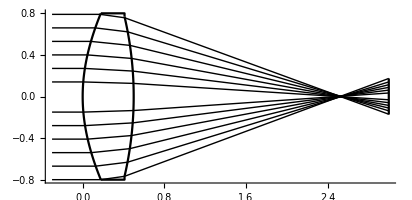

```mathematica
Show[rayCongruenceGraphics[rs,removeLast->False,rayCount->16],opticsGraphics[op,hideUselessSurface->False],Axes->True,ImageSize->Medium]
```